## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)

(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/parse/"; 
Needspaclet:ref/Needs["PhysicalConstants`"];Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.431717 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Jan 25, 2020, time: 09:50:16

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/parse/mercury mom parser 04.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.431717 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
c=299792458;
```

#### functions

#### substitutions

#### modules

## 1 point to data

```mathematica
dirMoM="/Users/dantopa/Dropbox/2nd-generation/RCS-project/linux/ubuntu/";
```

## 2 read data file

```mathematica
strmList=Import[dirMoM<>"sphereCourse.4112.txt","Data"]
Λ=Dimensions[strmList]
```

{ ,---| Run Date: January   21, 2020;    Time: 13:09:36,51907,--------------------------------------------------------------------------------}
 |  |  |  |

{51910}

## 3 mark data sets

```mathematica
(* each data set represents a unique frequency *)
```

```mathematica
census={};
Table[
If[StringContainsQ[strmList[[k]],"  Freq   ="],AppendTo[census,k]]
,{k,Length[strmList]}];
census
m=Length[census]
```

{486,1001,1516,2031,2546,3061,3576,4091,4606,5121,5636,6151,6666,7181,7696,8211,8726,9241,9756,10271,10786,11301,11816,12331,12846,13361,13876,14391,14906,15421,15936,16451,16966,17481,17996,18511,19026,19541,20056,20571,21086,21601,22116,22631,23146,23661,24176,24691,25206,25721,26236,26751,27266,27781,28296,28811,29326,29841,30356,30871,31386,31901,32416,32931,33446,33961,34476,34991,35506,36021,36536,37051,37566,38081,38596,39111,39626,40141,40656,41171,41686,42201,42716,43231,43746,44261,44776,45291,45806,46321,46836,47351,47866,48381,48896,49411,49926,50441,50956,51471}

100

## 4 parse a line

```mathematica
(* sweep through the output file and convert the text to complex values for the electric field *)
```

### modules

```mathematica
λ=14; (* length of character string *)
```

```mathematica
Clear[strToNumber];
strToNumber[str_String]:=Module[{},
sign=1;
mant=StringTake[str,{2,10}];
exp=StringTake[str,{12,14}];
sig=StringTake[str,{1}];
If[sig=="-",sign=-1];
number=sign ToExpression[mant] 10^ToExpression[exp];
Return[number]
];
strToNumber[" 0.2332290E-01"]
```

0.0233229

```mathematica
Clear[grabComplex];
grabComplex[str_String]:=Module[{},
real=strToNumber[StringTake[str,{1,λ}]];
imag=strToNumber[StringTake[str,{λ+3,2λ+2}]];
Return[real+ⅈ imag]
];
grabComplex[" 0.2332290E-01, -0.8848302E-04"]
```

0.0233229-0.000088483 ⅈ

### test a line

```mathematica
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,485}];
```

```mathematica
Close[myStream]
```

/Users/dantopa/Dropbox/2nd-generation/RCS-project/linux/ubuntu/sphereCourse.4112.txt

```mathematica
α=29;
gap=34;
fields=4;
```

```mathematica
Table[
start=α+(k-1)gap;
grabComplex[StringTake[data,{start,start+2λ+2}]]
,{k,fields}]
```

{0.0233229-0.000088483 ⅈ,-0.000168663-2.62138×10^-6 ⅈ,-0.000168663-2.62956×10^-6 ⅈ,0.0227787-0.0000928122 ⅈ}

## 5 read a set

```mathematica
(* read a measurement for fixed ν: 0 - 360 degrees *)
```

```mathematica
lines={378,854};
ν=10000000;
```

```mathematica
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,lines[[1]]-1}]
```

```mathematica
tbl=Table[
data=ReadLine[myStream];
Table[
start=α+(k-1)gap;
grabComplex[StringTake[data,{start,start+2λ+2}]]
,{k,fields}]
,{j,0,360}];
```

```mathematica
Close[myStream];
```

```mathematica
Abs/@tbl
```

{{0.0233327,0.0000888454,0.0000888454,0.0227505},{0.0233329,0.0000862115,0.0000862098,0.0227495},{0.023333,0.0000835492,0.0000835489,0.0227486},{0.0233332,0.0000808622,0.0000808616,0.0227476},{0.0233333,0.0000781502,0.0000781495,0.0227467},{0.0233334,0.000075414,0.0000754135,0.0227457},{0.0233335,0.0000726521,0.0000726527,0.0227448},{0.0233337,0.000069871,0.0000698703,0.0227439},{0.0233338,0.0000670674,0.0000670663,0.0227431},{0.0233339,0.0000642428,0.0000642434,0.0227422},{0.023334,0.0000614005,0.0000613984,0.0227414},{0.0233341,0.0000585353,0.000058535,0.0227406},{0.0233341,0.0000556544,0.0000556528,0.0227398},{0.0233342,0.000052756,0.000052755,0.022739},{0.0233343,0.0000498425,0.0000498409,0.0227383},{0.0233343,0.000046912,0.0000469116,0.0227376},{0.0233344,0.0000439678,0.0000439679,0.0227369},{0.0233344,0.00004101,0.0000410109,0.0227362},{0.0233345,0.0000380411,0.0000380398,0.0227356},{0.0233345,0.0000350604,0.0000350599,0.022735},{0.0233345,0.0000320681,0.0000320681,0.0227344},{0.0233346,0.0000290663,0.000029066,0.0227339},{0.0233346,0.0000260557,0.0000260554,0.0227333},{0.0233346,0.000023039,0.0000230385,0.0227329},{0.0233345,0.000020015,0.0000200145,0.0227324},{0.0233345,0.000016985,0.0000169838,0.022732},{0.0233345,0.0000139503,0.0000139493,0.0227316},{0.0233345,0.0000109121,0.000010911,0.0227312},{0.0233344,7.87132×10^-6,7.86988×10^-6,0.0227309},{0.0233344,4.82664×10^-6,4.82675×10^-6,0.0227306},{0.0233344,1.78618×10^-6,1.78671×10^-6,0.0227303},{0.0233343,1.275×10^-6,1.27464×10^-6,0.0227301},{0.0233342,4.31227×10^-6,4.31263×10^-6,0.0227299},{0.0233342,7.3535×10^-6,7.35326×10^-6,0.0227298},{0.0233341,0.0000103918,0.0000103926,0.0227296},{0.023334,0.0000134281,0.000013428,0.0227295},{0.0233339,0.0000164592,0.000016459,0.0227295},{0.0233338,0.0000194834,0.0000194833,0.0227294},{0.0233337,0.0000225024,0.0000225031,0.0227295},{0.0233336,0.0000255137,0.0000255143,0.0227295},{0.0233335,0.0000285171,0.0000285167,0.0227296},{0.0233334,0.0000315099,0.0000315105,0.0227297},{0.0233333,0.0000344937,0.0000344925,0.0227298},{0.0233331,0.0000374657,0.0000374654,0.02273},{0.023333,0.0000404249,0.0000404253,0.0227302},{0.0233329,0.0000433736,0.0000433719,0.0227304},{0.0233327,0.0000463048,0.0000463054,0.0227307},{0.0233326,0.0000492223,0.0000492238,0.022731},{0.0233324,0.0000521259,0.0000521265,0.0227313},{0.0233323,0.0000550121,0.0000550114,0.0227317},{0.0233321,0.0000578811,0.00005788,0.0227321},{0.0233319,0.0000607305,0.0000607315,0.0227325},{0.0233318,0.0000635624,0.0000635625,0.022733},{0.0233316,0.0000663743,0.0000663731,0.0227335},{0.0233314,0.0000691629,0.0000691627,0.022734},{0.0233313,0.0000719322,0.0000719323,0.0227345},{0.0233311,0.0000746788,0.0000746805,0.0227351},{0.0233309,0.000077402,0.0000774018,0.0227357},{0.0233307,0.0000800999,0.0000800995,0.0227363},{0.0233306,0.0000827744,0.0000827733,0.0227369},{0.0233304,0.0000854224,0.0000854222,0.0227376},{0.0233302,0.0000880441,0.000088043,0.0227383},{0.02333,0.0000906366,0.0000906369,0.022739},{0.0233298,0.000093204,0.0000932034,0.0227397},{0.0233296,0.0000957412,0.0000957402,0.0227405},{0.0233294,0.0000982491,0.0000982486,0.0227412},{0.0233292,0.000100726,0.000100726,0.022742},{0.0233291,0.000103173,0.000103172,0.0227428},{0.0233289,0.000105587,0.000105587,0.0227437},{0.0233287,0.000107969,0.00010797,0.0227445},{0.0233285,0.000110319,0.000110319,0.0227454},{0.0233283,0.000112636,0.000112635,0.0227463},{0.0233281,0.000114915,0.000114916,0.0227471},{0.0233279,0.000117161,0.000117162,0.0227481},{0.0233277,0.000119371,0.000119372,0.022749},{0.0233275,0.000121546,0.000121544,0.0227499},{0.0233273,0.000123683,0.000123682,0.0227508},{0.0233272,0.000125781,0.000125781,0.0227518},{0.023327,0.000127842,0.000127843,0.0227527},{0.0233268,0.000129864,0.000129865,0.0227537},{0.0233266,0.000131846,0.000131846,0.0227547},{0.0233264,0.00013379,0.00013379,0.0227556},{0.0233263,0.000135692,0.000135692,0.0227566},{0.0233261,0.000137552,0.000137554,0.0227576},{0.0233259,0.000139372,0.000139372,0.0227586},{0.0233257,0.000141148,0.000141149,0.0227595},{0.0233256,0.000142883,0.000142883,0.0227605},{0.0233254,0.000144575,0.000144574,0.0227615},{0.0233252,0.000146223,0.000146223,0.0227625},{0.0233251,0.000147826,0.000147827,0.0227634},{0.0233249,0.000149385,0.000149385,0.0227644},{0.0233248,0.000150899,0.000150898,0.0227654},{0.0233246,0.000152367,0.000152367,0.0227663},{0.0233245,0.00015379,0.000153791,0.0227672},{0.0233244,0.000155167,0.000155167,0.0227682},{0.0233242,0.000156496,0.000156497,0.0227691},{0.0233241,0.000157778,0.000157778,0.02277},{0.023324,0.000159015,0.000159014,0.0227709},{0.0233239,0.000160201,0.000160202,0.0227718},{0.0233238,0.000161341,0.000161342,0.0227726},{0.0233237,0.00016243,0.000162432,0.0227735},{0.0233236,0.000163473,0.000163474,0.0227743},{0.0233235,0.000164466,0.000164466,0.0227751},{0.0233234,0.00016541,0.000165408,0.0227759},{0.0233233,0.000166303,0.000166303,0.0227767},{0.0233232,0.000167146,0.000167147,0.0227775},{0.0233231,0.000167941,0.00016794,0.0227782},{0.0233231,0.000168683,0.000168684,0.0227789},{0.023323,0.000169375,0.000169376,0.0227796},{0.0233229,0.000170017,0.000170017,0.0227802},{0.0233229,0.000170607,0.000170607,0.0227809},{0.0233229,0.000171146,0.000171147,0.0227815},{0.0233228,0.000171634,0.000171634,0.022782},{0.0233228,0.00017207,0.000172069,0.0227826},{0.0233228,0.000172454,0.000172454,0.0227831},{0.0233228,0.000172786,0.000172787,0.0227836},{0.0233228,0.000173067,0.000173066,0.022784},{0.0233228,0.000173294,0.000173294,0.0227845},{0.0233228,0.00017347,0.000173471,0.0227848},{0.0233228,0.000173594,0.000173593,0.0227852},{0.0233228,0.000173664,0.000173666,0.0227855},{0.0233228,0.000173684,0.000173684,0.0227858},{0.0233229,0.000173649,0.000173649,0.0227861},{0.0233229,0.000173564,0.000173564,0.0227863},{0.023323,0.000173424,0.000173425,0.0227865},{0.023323,0.000173234,0.000173233,0.0227866},{0.0233231,0.000172991,0.000172991,0.0227867},{0.0233232,0.000172695,0.000172695,0.0227868},{0.0233232,0.000172346,0.000172347,0.0227869},{0.0233233,0.000171946,0.000171946,0.0227869},{0.0233234,0.000171493,0.000171494,0.0227868},{0.0233235,0.00017099,0.00017099,0.0227868},{0.0233236,0.000170433,0.000170432,0.0227867},{0.0233238,0.000169825,0.000169824,0.0227865},{0.0233239,0.000169164,0.000169164,0.0227863},{0.023324,0.000168452,0.000168452,0.0227861},{0.0233241,0.00016769,0.00016769,0.0227859},{0.0233243,0.000166875,0.000166876,0.0227856},{0.0233244,0.00016601,0.000166011,0.0227853},{0.0233246,0.000165096,0.000165096,0.0227849},{0.0233247,0.00016413,0.000164131,0.0227845},{0.0233249,0.000163113,0.000163113,0.0227841},{0.0233251,0.000162047,0.000162049,0.0227837},{0.0233252,0.000160932,0.000160932,0.0227832},{0.0233254,0.000159768,0.000159767,0.0227826},{0.0233256,0.000158553,0.000158553,0.0227821},{0.0233258,0.000157292,0.00015729,0.0227815},{0.023326,0.00015598,0.000155979,0.0227809},{0.0233262,0.00015462,0.000154621,0.0227802},{0.0233264,0.000153215,0.000153215,0.0227796},{0.0233266,0.000151762,0.000151763,0.0227789},{0.0233268,0.000150264,0.000150261,0.0227781},{0.023327,0.000148715,0.000148715,0.0227774},{0.0233272,0.000147123,0.000147124,0.0227766},{0.0233274,0.000145485,0.000145485,0.0227758},{0.0233276,0.000143803,0.000143803,0.022775},{0.0233279,0.000142077,0.000142076,0.0227741},{0.0233281,0.000140305,0.000140306,0.0227733},{0.0233283,0.000138492,0.000138491,0.0227724},{0.0233285,0.000136635,0.000136633,0.0227715},{0.0233287,0.000134735,0.000134735,0.0227705},{0.023329,0.000132795,0.000132795,0.0227696},{0.0233292,0.000130814,0.000130813,0.0227687},{0.0233294,0.00012879,0.00012879,0.0227677},{0.0233296,0.000126728,0.000126728,0.0227667},{0.0233298,0.000124626,0.000124625,0.0227657},{0.02333,0.000122486,0.000122484,0.0227647},{0.0233303,0.000120306,0.000120306,0.0227637},{0.0233305,0.000118091,0.000118091,0.0227627},{0.0233307,0.000115838,0.000115839,0.0227617},{0.0233309,0.00011355,0.000113549,0.0227607},{0.0233311,0.000111226,0.000111227,0.0227596},{0.0233313,0.000108869,0.000108869,0.0227586},{0.0233315,0.000106476,0.000106476,0.0227576},{0.0233317,0.000104051,0.000104051,0.0227566},{0.0233319,0.000101594,0.000101594,0.0227555},{0.023332,0.0000991053,0.0000991038,0.0227545},{0.0233322,0.0000965852,0.000096584,0.0227535},{0.0233324,0.0000940354,0.0000940365,0.0227525},{0.0233326,0.0000914575,0.0000914575,0.0227515},{0.0233327,0.0000888486,0.0000888484,0.0227505},{0.0233329,0.0000862144,0.0000862145,0.0227495},{0.023333,0.0000835532,0.0000835533,0.0227486},{0.0233332,0.0000808656,0.0000808659,0.0227476},{0.0233333,0.000078153,0.0000781537,0.0227467},{0.0233334,0.000075418,0.0000754177,0.0227458},{0.0233336,0.0000726565,0.0000726578,0.0227448},{0.0233337,0.0000698745,0.0000698744,0.022744},{0.0233338,0.0000670703,0.0000670692,0.0227431},{0.0233339,0.0000642457,0.0000642458,0.0227422},{0.023334,0.0000614006,0.0000614025,0.0227414},{0.0233341,0.0000585371,0.0000585384,0.0227406},{0.0233342,0.0000556561,0.0000556571,0.0227398},{0.0233342,0.0000527578,0.0000527588,0.022739},{0.0233343,0.0000498434,0.0000498442,0.0227383},{0.0233344,0.0000469138,0.0000469145,0.0227376},{0.0233344,0.0000439695,0.0000439697,0.0227369},{0.0233344,0.0000410138,0.0000410123,0.0227362},{0.0233345,0.0000380417,0.0000380428,0.0227356},{0.0233345,0.0000350613,0.0000350614,0.022735},{0.0233345,0.0000320699,0.0000320703,0.0227344},{0.0233346,0.0000290688,0.0000290685,0.0227339},{0.0233346,0.0000260574,0.0000260573,0.0227333},{0.0233346,0.0000230408,0.0000230401,0.0227329},{0.0233346,0.0000200153,0.0000200155,0.0227324},{0.0233345,0.0000169854,0.0000169857,0.022732},{0.0233345,0.0000139497,0.0000139505,0.0227316},{0.0233345,0.0000109108,0.0000109117,0.0227312},{0.0233344,7.86898×10^-6,7.86963×10^-6,0.0227309},{0.0233344,4.8262×10^-6,4.82796×10^-6,0.0227306},{0.0233344,1.78709×10^-6,1.78708×10^-6,0.0227303},{0.0233343,1.27642×10^-6,1.27528×10^-6,0.0227301},{0.0233342,4.31408×10^-6,4.3127×10^-6,0.0227299},{0.0233342,7.35366×10^-6,7.35438×10^-6,0.0227297},{0.0233341,0.0000103935,0.0000103933,0.0227296},{0.023334,0.0000134293,0.0000134282,0.0227295},{0.0233339,0.0000164605,0.0000164603,0.0227295},{0.0233338,0.0000194866,0.000019486,0.0227294},{0.0233337,0.0000225046,0.000022503,0.0227294},{0.0233336,0.0000255163,0.0000255152,0.0227295},{0.0233335,0.0000285182,0.0000285188,0.0227296},{0.0233334,0.0000315125,0.0000315127,0.0227297},{0.0233333,0.0000344949,0.0000344961,0.0227298},{0.0233331,0.0000374668,0.0000374681,0.02273},{0.023333,0.0000404272,0.0000404287,0.0227302},{0.0233329,0.0000433736,0.0000433742,0.0227304},{0.0233327,0.0000463089,0.0000463078,0.0227307},{0.0233326,0.0000492272,0.0000492269,0.022731},{0.0233324,0.0000521289,0.0000521296,0.0227313},{0.0233323,0.000055016,0.0000550157,0.0227317},{0.0233321,0.0000578838,0.0000578856,0.0227321},{0.0233319,0.0000607344,0.000060735,0.0227325},{0.0233318,0.0000635662,0.0000635655,0.022733},{0.0233316,0.0000663772,0.0000663774,0.0227335},{0.0233314,0.0000691676,0.0000691678,0.022734},{0.0233313,0.0000719365,0.0000719369,0.0227345},{0.0233311,0.0000746826,0.0000746838,0.0227351},{0.0233309,0.0000774053,0.0000774061,0.0227357},{0.0233307,0.0000801051,0.0000801053,0.0227363},{0.0233306,0.0000827772,0.0000827778,0.0227369},{0.0233304,0.0000854258,0.0000854267,0.0227376},{0.0233302,0.0000880479,0.0000880482,0.0227383},{0.02333,0.0000906444,0.0000906417,0.022739},{0.0233298,0.0000932096,0.0000932099,0.0227397},{0.0233296,0.0000957464,0.0000957466,0.0227405},{0.0233294,0.0000982541,0.0000982546,0.0227412},{0.0233292,0.000100731,0.000100732,0.022742},{0.023329,0.000103178,0.000103179,0.0227428},{0.0233289,0.000105593,0.000105593,0.0227437},{0.0233287,0.000107977,0.000107975,0.0227445},{0.0233285,0.000110326,0.000110326,0.0227454},{0.0233283,0.000112641,0.000112641,0.0227463},{0.0233281,0.000114923,0.000114922,0.0227471},{0.0233279,0.000117169,0.000117168,0.0227481},{0.0233277,0.000119379,0.000119378,0.022749},{0.0233275,0.000121552,0.000121552,0.0227499},{0.0233273,0.000123689,0.000123689,0.0227508},{0.0233272,0.000125789,0.000125788,0.0227518},{0.023327,0.00012785,0.000127848,0.0227527},{0.0233268,0.000129871,0.00012987,0.0227537},{0.0233266,0.000131853,0.000131853,0.0227547},{0.0233264,0.000133796,0.000133796,0.0227556},{0.0233263,0.000135698,0.000135698,0.0227566},{0.0233261,0.00013756,0.000137558,0.0227576},{0.0233259,0.000139378,0.000139378,0.0227586},{0.0233257,0.000141155,0.000141155,0.0227595},{0.0233256,0.000142892,0.000142891,0.0227605},{0.0233254,0.000144582,0.00014458,0.0227615},{0.0233253,0.000146228,0.000146229,0.0227625},{0.0233251,0.000147832,0.000147832,0.0227634},{0.0233249,0.000149393,0.000149392,0.0227644},{0.0233248,0.000150906,0.000150905,0.0227654},{0.0233247,0.000152373,0.000152375,0.0227663},{0.0233245,0.000153796,0.000153797,0.0227672},{0.0233244,0.000155172,0.000155172,0.0227682},{0.0233243,0.000156502,0.000156501,0.0227691},{0.0233241,0.000157784,0.000157784,0.02277},{0.023324,0.000159019,0.000159019,0.0227709},{0.0233239,0.000160206,0.000160207,0.0227718},{0.0233238,0.000161346,0.000161346,0.0227726},{0.0233237,0.000162437,0.000162437,0.0227735},{0.0233236,0.000163478,0.000163478,0.0227743},{0.0233235,0.000164471,0.000164471,0.0227751},{0.0233234,0.000165414,0.000165414,0.0227759},{0.0233233,0.000166308,0.000166308,0.0227767},{0.0233232,0.000167152,0.000167151,0.0227775},{0.0233231,0.000167945,0.000167945,0.0227782},{0.0233231,0.000168688,0.000168688,0.0227789},{0.023323,0.00016938,0.00016938,0.0227796},{0.023323,0.000170022,0.000170021,0.0227802},{0.0233229,0.000170612,0.000170612,0.0227809},{0.0233229,0.00017115,0.00017115,0.0227815},{0.0233228,0.000171636,0.000171637,0.022782},{0.0233228,0.000172073,0.000172073,0.0227826},{0.0233228,0.000172457,0.000172457,0.0227831},{0.0233228,0.000172789,0.000172789,0.0227836},{0.0233228,0.00017307,0.000173069,0.022784},{0.0233228,0.000173297,0.000173297,0.0227845},{0.0233228,0.000173473,0.000173472,0.0227849},{0.0233228,0.000173596,0.000173596,0.0227852},{0.0233228,0.000173667,0.000173668,0.0227855},{0.0233228,0.000173685,0.000173687,0.0227858},{0.0233229,0.000173651,0.000173653,0.0227861},{0.0233229,0.000173565,0.000173567,0.0227863},{0.023323,0.000173427,0.000173428,0.0227865},{0.023323,0.000173236,0.000173235,0.0227866},{0.0233231,0.000172992,0.000172992,0.0227867},{0.0233232,0.000172696,0.000172695,0.0227868},{0.0233232,0.000172347,0.000172347,0.0227869},{0.0233233,0.000171947,0.000171947,0.0227869},{0.0233234,0.000171494,0.000171494,0.0227868},{0.0233235,0.000170988,0.000170989,0.0227868},{0.0233236,0.000170432,0.000170433,0.0227867},{0.0233238,0.000169824,0.000169824,0.0227865},{0.0233239,0.000169164,0.000169163,0.0227864},{0.023324,0.000168452,0.000168453,0.0227861},{0.0233241,0.000167689,0.00016769,0.0227859},{0.0233243,0.000166877,0.000166875,0.0227856},{0.0233244,0.000166011,0.00016601,0.0227853},{0.0233246,0.000165095,0.000165095,0.0227849},{0.0233247,0.000164129,0.000164129,0.0227845},{0.0233249,0.000163112,0.000163112,0.0227841},{0.0233251,0.000162047,0.000162046,0.0227837},{0.0233252,0.000160931,0.00016093,0.0227832},{0.0233254,0.000159765,0.000159765,0.0227827},{0.0233256,0.000158551,0.000158552,0.0227821},{0.0233258,0.000157289,0.000157289,0.0227815},{0.023326,0.000155977,0.000155978,0.0227809},{0.0233262,0.000154619,0.000154618,0.0227802},{0.0233264,0.000153212,0.000153213,0.0227796},{0.0233266,0.000151759,0.000151759,0.0227789},{0.0233268,0.000150259,0.00015026,0.0227781},{0.023327,0.000148713,0.000148714,0.0227774},{0.0233272,0.000147121,0.00014712,0.0227766},{0.0233274,0.000145482,0.000145483,0.0227758},{0.0233276,0.0001438,0.0001438,0.022775},{0.0233279,0.000142073,0.000142072,0.0227741},{0.0233281,0.000140302,0.000140301,0.0227733},{0.0233283,0.000138487,0.000138487,0.0227724},{0.0233285,0.00013663,0.000136631,0.0227715},{0.0233287,0.00013473,0.000134731,0.0227705},{0.023329,0.000132789,0.00013279,0.0227696},{0.0233292,0.000130806,0.000130808,0.0227687},{0.0233294,0.000128785,0.000128785,0.0227677},{0.0233296,0.000126722,0.000126722,0.0227667},{0.0233298,0.00012462,0.000124622,0.0227657},{0.02333,0.000122481,0.000122482,0.0227647},{0.0233302,0.000120302,0.000120302,0.0227637},{0.0233305,0.000118086,0.000118086,0.0227627},{0.0233307,0.000115835,0.000115835,0.0227617},{0.0233309,0.000113546,0.000113545,0.0227607},{0.0233311,0.000111223,0.000111222,0.0227596},{0.0233313,0.000108864,0.000108863,0.0227586},{0.0233315,0.000106472,0.000106472,0.0227576},{0.0233317,0.000104047,0.000104047,0.0227566},{0.0233318,0.00010159,0.00010159,0.0227555},{0.023332,0.0000990999,0.0000991003,0.0227545},{0.0233322,0.0000965811,0.0000965809,0.0227535},{0.0233324,0.0000940315,0.0000940322,0.0227525},{0.0233325,0.0000914526,0.0000914528,0.0227515},{0.0233327,0.0000888451,0.0000888447,0.0227505}}

## 6 tag sets

```mathematica
ω=378;
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,ω}];
Print["ω = "ω,lf,data];
Close[myStream];
```

378 ω = 
     90.0000,      0.0000,(  0.2333228E-01,  0.1410688E-03),(  0.8868390E-04,  0.5353989E-05),(  0.8868393E-04,  0.5354086E-05),(  0.2275015E-01,  0.1270486E-03)

```mathematica
ω=845;
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,ω}];
Print["ω = "ω,lf,data];
Close[myStream];
```

845 ω = 
     90.0000,      0.0000,(  0.9314477E-01,  0.9381430E-03),(  0.3635161E-03,  0.4137083E-04),(  0.3635184E-03,  0.4137683E-04),(  0.9076662E-01,  0.8370526E-03)

```mathematica
845-378
```

467

```mathematica
ω=845+467;
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,ω}];
Print["ω = "ω,lf,data];
Close[myStream];
```

1312 ω = 
     90.0000,      0.0000,(  0.2088588E+00,  0.2012354E-02),(  0.8537174E-03,  0.1293710E-03),(  0.8537163E-03,  0.1294172E-03),(  0.2033185E+00,  0.1744069E-02)

```mathematica
ω=845+2 467;
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,ω}];
Print["ω = "ω,lf,data];
Close[myStream];
```

1779 ω = 
     90.0000,      0.0000,(  0.3691945E+00,  0.5851295E-03),(  0.1608609E-02,  0.2657743E-03),(  0.1608598E-02,  0.2658021E-03),(  0.3588777E+00,  0.2352974E-03)

```mathematica
start=378;
jump=467;
Do[
Print[start," + ",k," × ",jump," = ",start + k jump]
,{k,0,99}]
```

378 + 0 × 467 = 378

378 + 1 × 467 = 845

378 + 2 × 467 = 1312

378 + 3 × 467 = 1779

378 + 4 × 467 = 2246

378 + 5 × 467 = 2713

378 + 6 × 467 = 3180

378 + 7 × 467 = 3647

378 + 8 × 467 = 4114

378 + 9 × 467 = 4581

378 + 10 × 467 = 5048

378 + 11 × 467 = 5515

378 + 12 × 467 = 5982

378 + 13 × 467 = 6449

378 + 14 × 467 = 6916

378 + 15 × 467 = 7383

378 + 16 × 467 = 7850

378 + 17 × 467 = 8317

378 + 18 × 467 = 8784

378 + 19 × 467 = 9251

378 + 20 × 467 = 9718

378 + 21 × 467 = 10185

378 + 22 × 467 = 10652

378 + 23 × 467 = 11119

378 + 24 × 467 = 11586

378 + 25 × 467 = 12053

378 + 26 × 467 = 12520

378 + 27 × 467 = 12987

378 + 28 × 467 = 13454

378 + 29 × 467 = 13921

378 + 30 × 467 = 14388

378 + 31 × 467 = 14855

378 + 32 × 467 = 15322

378 + 33 × 467 = 15789

378 + 34 × 467 = 16256

378 + 35 × 467 = 16723

378 + 36 × 467 = 17190

378 + 37 × 467 = 17657

378 + 38 × 467 = 18124

378 + 39 × 467 = 18591

378 + 40 × 467 = 19058

378 + 41 × 467 = 19525

378 + 42 × 467 = 19992

378 + 43 × 467 = 20459

378 + 44 × 467 = 20926

378 + 45 × 467 = 21393

378 + 46 × 467 = 21860

378 + 47 × 467 = 22327

378 + 48 × 467 = 22794

378 + 49 × 467 = 23261

378 + 50 × 467 = 23728

378 + 51 × 467 = 24195

378 + 52 × 467 = 24662

378 + 53 × 467 = 25129

378 + 54 × 467 = 25596

378 + 55 × 467 = 26063

378 + 56 × 467 = 26530

378 + 57 × 467 = 26997

378 + 58 × 467 = 27464

378 + 59 × 467 = 27931

378 + 60 × 467 = 28398

378 + 61 × 467 = 28865

378 + 62 × 467 = 29332

378 + 63 × 467 = 29799

378 + 64 × 467 = 30266

378 + 65 × 467 = 30733

378 + 66 × 467 = 31200

378 + 67 × 467 = 31667

378 + 68 × 467 = 32134

378 + 69 × 467 = 32601

378 + 70 × 467 = 33068

378 + 71 × 467 = 33535

378 + 72 × 467 = 34002

378 + 73 × 467 = 34469

378 + 74 × 467 = 34936

378 + 75 × 467 = 35403

378 + 76 × 467 = 35870

378 + 77 × 467 = 36337

378 + 78 × 467 = 36804

378 + 79 × 467 = 37271

378 + 80 × 467 = 37738

378 + 81 × 467 = 38205

378 + 82 × 467 = 38672

378 + 83 × 467 = 39139

378 + 84 × 467 = 39606

378 + 85 × 467 = 40073

378 + 86 × 467 = 40540

378 + 87 × 467 = 41007

378 + 88 × 467 = 41474

378 + 89 × 467 = 41941

378 + 90 × 467 = 42408

378 + 91 × 467 = 42875

378 + 92 × 467 = 43342

378 + 93 × 467 = 43809

378 + 94 × 467 = 44276

378 + 95 × 467 = 44743

378 + 96 × 467 = 45210

378 + 97 × 467 = 45677

378 + 98 × 467 = 46144

378 + 99 × 467 = 46611

```mathematica
ω=378+99 467;
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
Do[
data=ReadLine[myStream]
,{k,ω}];
Print["ω = "ω,lf,data];
Close[myStream];
```

46611 ω = 
     90.0000,      0.0000,(  0.2885610E+00, -0.1011976E+01),(  0.5899617E+00, -0.4689567E+00),(  0.5899619E+00, -0.4689569E+00),( -0.7161536E+00,  0.3769876E+00)

## read all

```mathematica
start=378;
jump=106;
```

```mathematica
θθ={};
θϕ={};
ϕθ={};
ϕϕ={};
```

```mathematica
myStream=OpenRead[dirMoM<>"sphereCourse.4112.txt"];
(* position pointer *)
Do[
ReadLine[myStream]
,{k,start-1}];
```

```mathematica
set=0;
While[set<100,
tbl=Table[
data=ReadLine[myStream];
Table[
start=α+(k-1)gap;
grabComplex[StringTake[data,{start,start+2λ+2}]]
,{k,fields}]
,{j,0,360}];
Print["* * * loaded efield values: set = ",set];

AppendTo[θθ,tbl[[All,1]]];
AppendTo[θϕ,tbl[[All,2]]];
AppendTo[ϕθ,tbl[[All,3]]];
AppendTo[ϕϕ,tbl[[All,4]]];

Do[
ReadLine[myStream];
(* Print[StringTake[ReadLine[myStream],10]] *)
,{k,jump}];
set++];
```

* * * loaded efield values: set = 0

* * * loaded efield values: set = 1

* * * loaded efield values: set = 2

* * * loaded efield values: set = 3

* * * loaded efield values: set = 4

* * * loaded efield values: set = 5

* * * loaded efield values: set = 6

* * * loaded efield values: set = 7

* * * loaded efield values: set = 8

* * * loaded efield values: set = 9

* * * loaded efield values: set = 10

* * * loaded efield values: set = 11

* * * loaded efield values: set = 12

* * * loaded efield values: set = 13

* * * loaded efield values: set = 14

* * * loaded efield values: set = 15

* * * loaded efield values: set = 16

* * * loaded efield values: set = 17

* * * loaded efield values: set = 18

* * * loaded efield values: set = 19

* * * loaded efield values: set = 20

* * * loaded efield values: set = 21

* * * loaded efield values: set = 22

* * * loaded efield values: set = 23

* * * loaded efield values: set = 24

* * * loaded efield values: set = 25

* * * loaded efield values: set = 26

* * * loaded efield values: set = 27

* * * loaded efield values: set = 28

* * * loaded efield values: set = 29

* * * loaded efield values: set = 30

* * * loaded efield values: set = 31

* * * loaded efield values: set = 32

* * * loaded efield values: set = 33

* * * loaded efield values: set = 34

* * * loaded efield values: set = 35

* * * loaded efield values: set = 36

* * * loaded efield values: set = 37

* * * loaded efield values: set = 38

* * * loaded efield values: set = 39

* * * loaded efield values: set = 40

* * * loaded efield values: set = 41

* * * loaded efield values: set = 42

* * * loaded efield values: set = 43

* * * loaded efield values: set = 44

* * * loaded efield values: set = 45

* * * loaded efield values: set = 46

* * * loaded efield values: set = 47

* * * loaded efield values: set = 48

* * * loaded efield values: set = 49

* * * loaded efield values: set = 50

* * * loaded efield values: set = 51

* * * loaded efield values: set = 52

* * * loaded efield values: set = 53

* * * loaded efield values: set = 54

* * * loaded efield values: set = 55

* * * loaded efield values: set = 56

* * * loaded efield values: set = 57

* * * loaded efield values: set = 58

* * * loaded efield values: set = 59

* * * loaded efield values: set = 60

* * * loaded efield values: set = 61

* * * loaded efield values: set = 62

* * * loaded efield values: set = 63

* * * loaded efield values: set = 64

* * * loaded efield values: set = 65

* * * loaded efield values: set = 66

* * * loaded efield values: set = 67

* * * loaded efield values: set = 68

* * * loaded efield values: set = 69

* * * loaded efield values: set = 70

* * * loaded efield values: set = 71

* * * loaded efield values: set = 72

* * * loaded efield values: set = 73

* * * loaded efield values: set = 74

* * * loaded efield values: set = 75

* * * loaded efield values: set = 76

* * * loaded efield values: set = 77

* * * loaded efield values: set = 78

* * * loaded efield values: set = 79

* * * loaded efield values: set = 80

* * * loaded efield values: set = 81

* * * loaded efield values: set = 82

* * * loaded efield values: set = 83

* * * loaded efield values: set = 84

* * * loaded efield values: set = 85

* * * loaded efield values: set = 86

* * * loaded efield values: set = 87

* * * loaded efield values: set = 88

* * * loaded efield values: set = 89

* * * loaded efield values: set = 90

* * * loaded efield values: set = 91

* * * loaded efield values: set = 92

* * * loaded efield values: set = 93

* * * loaded efield values: set = 94

* * * loaded efield values: set = 95

* * * loaded efield values: set = 96

* * * loaded efield values: set = 97

* * * loaded efield values: set = 98

* * * loaded efield values: set = 99

```mathematica
Dimensions[θθ]
```

{100,361}

## Plots -at last

```mathematica
vv=Map[Abs,θθ,2];
vh=Map[Abs,θθ,2];
hv=Map[Abs,θθ,2];
hh=Map[Abs,θθ,2];
```

{{0.0233327,0.0233329,0.023333,0.0233332,353,0.0233322,0.0233324,0.0233325,0.0233327},99}
 |  |  |  |

```mathematica
νticks={{1,100},{25,75},{50,50},{75,25},{100,1}};
λticks={{11.06,1},{71.02,10},{98.00,100}};θticks={o,{90,π/4},{180,π/2},{270,(3π)/4},{360,2π}};
θticks={{1,0},{91,90},{181,180},{271,270},{361,360}};
```

```mathematica
mp=MatrixPlot[Reverse[array],
AspectRatio->0.5,
ColorFunction->Hue,
FrameLabel->{{"θ",Null},{"ν (MHz)","λ (m)"}},
PlotLabel->"Sphere "<>lf<>"Energy Magnitude (Vertical in - Vertical out)",FrameTicks->{{νticks,λticks},{θticks,None}}]
```

```mathematica
tresExport["sphereCourse.4112 radar energy return",mp]
```

### array 2

```mathematica
θϕ[[1,1]]
```

0.0000886839+5.35399×10^-6 ⅈ

```mathematica
array2=Map[Abs,θϕ,2]
```

```mathematica
mp2=MatrixPlot[Reverse[array2],
AspectRatio->0.5,
ColorFunction->Hue,
FrameLabel->{{"θ",Null},{"ν (MHz)","λ (m)"}},
PlotLabel->"Sphere "<>lf<>"Energy Magnitude (Vertical in - Horizontal out)",FrameTicks->{{νticks,λticks},{θticks,None}}]
```

## plotsalot

```mathematica
Clear[myPlot];
myPlot[ψ_,str_String]:=Module[{},
g=MatrixPlot[Reverse[ψ],
AspectRatio->0.5,
ColorFunction->Hue,
FrameLabel->{{"θ",Null},{"ν (MHz)","λ (m)"}},
PlotLabel->"Sphere"<>lf<>str,FrameTicks->{{νticks,λticks},{θticks,None}}];
Return[g];
]
```

```mathematica
θticks={0,90,180,270,360};
```

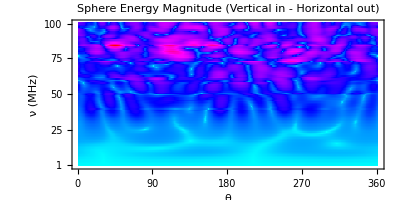

```mathematica
g002=myPlot[array2,"Energy Magnitude (Vertical in - Horizontal out)"]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```